```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/m0/m0_600/lowmub

```mathematica
chi0=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi0.dat"]],{i,0,800,10}];
chi1=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi1.dat"]],{i,0,800,10}];
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,0,800,10}];
chi3=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi3.dat"]],{i,0,800,10}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,0,800,10}];
r42=chi4/chi2//Quiet;
r21=chi2/chi1//Quiet;
r12=chi1/chi2//Quiet;
r32=chi3/chi2//Quiet;
r31=chi3/chi1//Quiet;
```

```mathematica
r42[[1;;45]][[1;;60]]=1;
r42[[46;;55]][[1;;50]]=1;
r42[[56;;62]][[1;;40]]=1;
r42[[63;;78]][[1;;20]]=1;
r42[[79;;80]][[1;;15]]=1;
(*r42[[85;;88]][[1;;10]]=1;*)
```

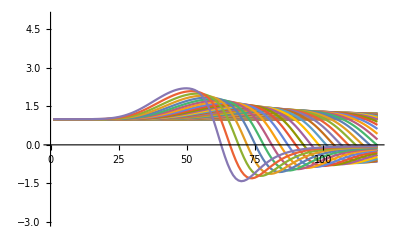

```mathematica
ListLinePlot[Table[r42[[i]],{i,1,80}],PlotRange->{All,{-3,5}}]
```

```mathematica
mub=Table[i,{i,0,800,10}];
T=Table[i,{i,1,120,1}];
```

```mathematica
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r42[[j]][[i]]},{i,1,120},{j,1,80}],1];
Export["r42low.dat",R42all]
```

r42low.dat

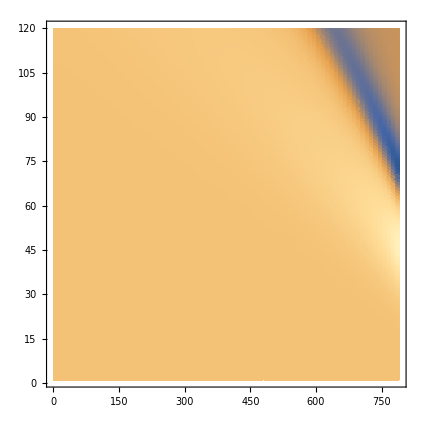

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-5,5}}]
```